```mathematica
Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
Table[j,{j,1,8,2}]
```

{1,3,5,7}

```mathematica
RandomInteger[{1,6},10]
```

{6,6,6,2,3,2,2,1,5,3}

```mathematica
dicerolls = RandomInteger[{1,6},10]
```

{1,5,6,2,6,5,6,2,6,2}

```mathematica
Mean[dicerolls]
```

41/10

```mathematica
1.9*Mean[dicerolls]
```

7.79

```mathematica
dicerolls=RandomInteger[{1,6},100000];
```

```mathematica
squares=Table[i^2,{i,1,8}]
```

{1,4,9,16,25,36,49,64}

```mathematica
upto8 = Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
Map[#^2 &, upto8]
```

{1,4,9,16,25,36,49,64}

```mathematica
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

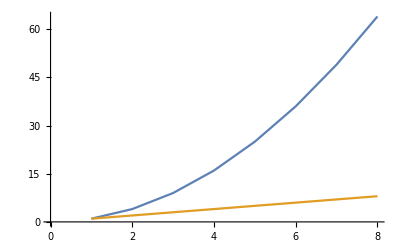

```mathematica
ListPlot[{squares,upto8},Joined->True]
```

```mathematica
Length[squares]
```

8

```mathematica
NestList[f,a,5]
```

{a,f[a],f[f[a]],f[f[f[a]]],f[f[f[f[a]]]],f[f[f[f[f[a]]]]]}

```mathematica
NestList[Riffle[Take[#,5],Drop[#,5]] &, {1,2,3,4,5,6,7,8,9,10},10]
```

{{1,2,3,4,5,6,7,8,9,10},{1,6,2,7,3,8,4,9,5,10},{1,8,6,4,2,9,7,5,3,10},{1,9,8,7,6,5,4,3,2,10},{1,5,9,4,8,3,7,2,6,10},{1,3,5,7,9,2,4,6,8,10},{1,2,3,4,5,6,7,8,9,10},{1,6,2,7,3,8,4,9,5,10},{1,8,6,4,2,9,7,5,3,10},{1,9,8,7,6,5,4,3,2,10},{1,5,9,4,8,3,7,2,6,10}}

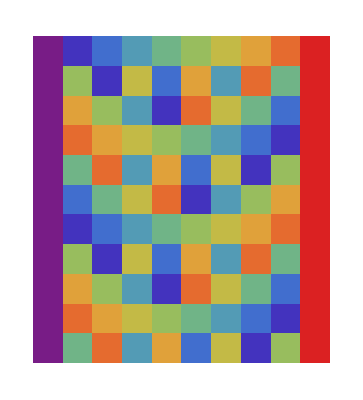

```mathematica
ArrayPlot[NestList[Riffle[Take[#,5],Drop[#,5]] &, {1,2,3,4,5,6,7,8,9,10},10],ColorFunction->"Rainbow"]
```

```mathematica
MatrixForm[{{1,2},{3,4}}]
```

(1 | 2
3 | 4)

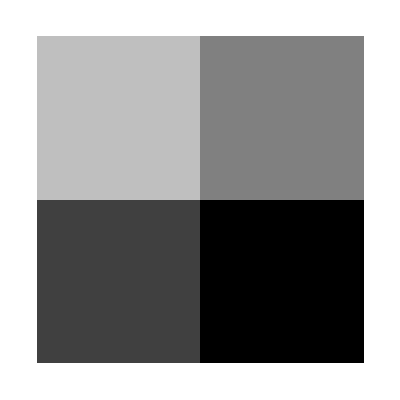

```mathematica
ArrayPlot[{{1,2},{3,4}}]
```

```mathematica
timestwoadd[x_]:=2*x+1
```

```mathematica
timestwoadd[4]
```

9

```mathematica
fn:=#*2+1 &
```

```mathematica
fn[4]
```

9

```mathematica
testifinputis7[x_]:=If[x==7,1,0]
```

```mathematica
testifinputis7[7]
```

1

```mathematica
Map[testifinputis7,Range[10]]
```

```mathematica
If[4>2,1,0]
```

1

```mathematica
Range[9]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
Map[Mod[#,5] &,Range[30]]
```

{1,2,3,4,0,1,2,3,4,0,1,2,3,4,0,1,2,3,4,0,1,2,3,4,0,1,2,3,4,0}

```mathematica
Map[{#,Mod[#,5]} &,Range[30]]
```

{{1,1},{2,2},{3,3},{4,4},{5,0},{6,1},{7,2},{8,3},{9,4},{10,0},{11,1},{12,2},{13,3},{14,4},{15,0},{16,1},{17,2},{18,3},{19,4},{20,0},{21,1},{22,2},{23,3},{24,4},{25,0},{26,1},{27,2},{28,3},{29,4},{30,0}}

```mathematica
Mod[21,5]
```

1

```mathematica
collatz[x_,y_]:=If[x==3*y||x==2*y+1||y==3*x||y==2*x+1,1,0]
```

```mathematica
Array[#^2 &, 10]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Array[#^2 &,{4,4}]
```

{{1,1,1,1},{4,4,4,4},{9,9,9,9},{16,16,16,16}}

```mathematica
Array[#1+2#2 &,{4,4}]
```

{{3,5,7,9},{4,6,8,10},{5,7,9,11},{6,8,10,12}}

```mathematica
Array[collatz[#1,#2] &, {20,20}]
```

{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
AdjacencyGraph[Array[collatz[#1,#2] &, {50,50}]]
```

```mathematica
GraphPlot3D[AdjacencyGraph[Array[collatz[#1,#2] &, {150,150}]]]
```

-Graphics3D-

```mathematica
Position[Map[Mod[#,7] &, Range[100]],6]
```

{{6},{13},{20},{27},{34},{41},{48},{55},{62},{69},{76},{83},{90},{97}}

```mathematica
Map[#[[1]] &,Position[Map[Mod[#,7] &, Range[100]],6]]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90,97}

```mathematica
Flatten[{{3,5,7,9},{4,6,8,10},{5,7,9,11},{6,8,10,12}}]
```

{3,5,7,9,4,6,8,10,5,7,9,11,6,8,10,12}

```mathematica
Select[Table[i,{i,1,10}],Mod[#,3]==0&]
```

{3,6,9}

```mathematica
Sort[RandomReal[{0,1},7],#1≥#2 &]
```

{0.950144,0.737792,0.722549,0.645544,0.334359,0.304272,0.19311}

```mathematica
"mystring"
```

mystring

```mathematica
StringJoin["dog","fish"]
```

dogfish

```mathematica
ToString[{3,5,7,9,4,6,8,10,5,7,9,11,6,8,10,12}]
```

{3, 5, 7, 9, 4, 6, 8, 10, 5, 7, 9, 11, 6, 8, 10, 12}

```mathematica
ToExpression["{3, 5, 7, 9, 4, 6, 8, 10, 5, 7, 9, 11, 6, 8, 10, 12}"]
```

{3,5,7,9,4,6,8,10,5,7,9,11,6,8,10,12}

```mathematica
StringSplit["{3, 5, 7, 9, 4, 6, 8, 10, 5, 7, 9, 11, 6, 8, 10, 12}","1"]
```

{{3, 5, 7, 9, 4, 6, 8, ,0, 5, 7, 9, ,,, 6, 8, ,0, ,2}}

```mathematica
StringReplace["{3, 5, 7, 9, 4, 6, 8, 10, 5, 7, 9, 11, 6, 8, 10, 12}","1"->"10"]
```

{3, 5, 7, 9, 4, 6, 8, 100, 5, 7, 9, 1010, 6, 8, 100, 102}

```mathematica
Characters["catfish"]
```

{c,a,t,f,i,s,h}

```mathematica
NestList[StringReplace[#,"110"->"100011101"] &,"110110110",5]
```

{110110110,100011101100011101100011101,100011000111011000111010011000111011000111010011000111011,100010001110100110001110110001110100110001110110010001110100110001110110001110100110001110110010001110100110001110111,100010001100011101100100011101001100011101100011101001100011101100100011101001100011101100011101010001100011101100100011101001100011101100011101001100011101100100011101001100011101100011101010001100011101100100011101001100011101111,100010001000111010011000111011000111010100011000111011001000111010011000111011000111010011000111011001000111010011000111011000111010100011000111011001000111010011000111011000111010011000111011010001000111010011000111011000111010100011000111011001000111010011000111011000111010011000111011001000111010011000111011000111010100011000111011001000111010011000111011000111010011000111011010001000111010011000111011000111010100011000111011001000111010011000111011111}

```mathematica
"110110110"
```

110110110

```mathematica
conv[x_]:=Map[If[#=="0",1,2] &,Characters[x]]
```

```mathematica
conv["110110110"]
```

{2,2,1,2,2,1,2,2,1}

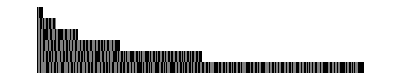

```mathematica
ArrayPlot[Map[conv,NestList[StringReplace[#,"110"->"100011101"] &,"110110110",5]]]
```

```mathematica
Module[{dog=9,cat=5},cat]
```

5